# Vaje za 2. teden

7. 3. 2024

## Ponovitev

Izračunaj 1+x+x^2+x^3, kjer je x = 1/√e+1/√π, na dva načina: naprej s pomočjo prepisovalnega pravila, nato pa še tako, da definiraš vrednost spremenljivke x.
Spremenljivko x na koncu pobriši.

```mathematica
x = (1/Sqrt[N[E]]) + 1/Sqrt[N[Pi]]
```

1.17072

```mathematica
1+x+x^2+x^3
```

5.14588

```mathematica
Sin[x/3]Cos[y/2] + Cos[x/3]Sin[y/2]// FullSimplify
```

Sin[1/6 (2 x+3 y)]

```mathematica
% /. {x -> Pi, y -> 4}
```

Sin[1/6 (12+2 π)]

```mathematica
Clear[x]
```

## Naloga 1

Izračunaj 1000-i decimalki števil e in π na dva načina:
1. Tako da izračunaš dovolj decimalk obeh števil in pogledaš ustrezno decimalko pri koncu. Zakaj zadnja decimalka ne bo v redu? Uporabi funkcijo N tako, da ji podaš natančnost.
2. Z uporabo funkcije RealDigits in izpisom ustreznega elementa seznama.

Določi še 5., 100. in 443. decimalko.

Napiši fuknkcijo, ki sprejme poljubno realno število x in naravno število n in vrne n-to decimalko števila x.

```mathematica
N[E,1001]
N[Pi, 1001]
```

2.7182818284590452353602874713526624977572470936999595749669676277240766303535475945713821785251664274274663919320030599218174135966290435729003342952605956307381323286279434907632338298807531952510190115738341879307021540891499348841675092447614606680822648001684774118537423454424371075390777449920695517027618386062613313845830007520449338265602976067371132007093287091274437470472306969772093101416928368190255151086574637721112523897844250569536967707854499699679468644549059879316368892300987931277361782154249992295763514822082698951936680331825288693984964651058209392398294887933203625094431173012381970684161403970198376793206832823764648042953118023287825098194558153017567173613320698112509961818815930416903515988885193458072738667385894228792284998920868058257492796104841984443634632449684875602336248270419786232090021609902353043699418491463140934317381436405462531520961836908887070167683964243781405927145635490613031072085103837505101157477041718986106873969655212671546889570350354

3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253421170679821480865132823066470938446095505822317253594081284811174502841027019385211055596446229489549303819644288109756659334461284756482337867831652712019091456485669234603486104543266482133936072602491412737245870066063155881748815209209628292540917153643678925903600113305305488204665213841469519415116094330572703657595919530921861173819326117931051185480744623799627495673518857527248912279381830119491298336733624406566430860213949463952247371907021798609437027705392171762931767523846748184676694051320005681271452635608277857713427577896091736371787214684409012249534301465495853710507922796892589235420199561121290219608640344181598136297747713099605187072113499999983729780499510597317328160963185950244594553469083026425223082533446850352619311881710100031378387528865875332083814206171776691473035982534904287554687311595628638823537875937519577818577805321712268066130019278766111959092164201989

```mathematica
Last[RealDigits[E, 10, 1000][[1]]]
Last[RealDigits[E, 10, 5][[1]]]
Last[RealDigits[E, 10, 100][[1]]]
Last[RealDigits[E, 10, 443][[1]]]
```

```mathematica
F[x_, n_]:= Last[RealDigits[x, 10,n][[1]]]
```

```mathematica
F[E,1000]
```

5

## Naloga 2

V Matematico vnesi izraz sin(π/8)+cos(π/8). Kaj Mathematica vrne? Nato poskusi ta izraz poenostaviti s primernim izrazom (končni rezultat se “lepo” izrazi s koreni).Definiraj niz niz, ki bo lepo predstavil in zapisal rešitev te naloge. Po klicu spremenljivke niz naj tako Mathematica izpiše spodnji niz, kjer naj bo niz “___” nadomeščen s pravim rezultatom.
"Vsota sin(π/8) + cos(π/8) je enaka ___."

```mathematica
odgovor = Sin[π/8] +Cos[π/8] // FullSimplify

niz = StringForm["Vsota sin(π/8) + cos(π/8) je enaka ``.", odgovor]
```

√(1+1/(√2))

Vsota sin(π/8) + cos(π/8) je enaka √(1+1/(√2)).

## Naloga 3

Napiši  funkcijo poenostaviInIzpisi, ki  bo  sprejela  izraz “izr”, ga  poenostavila  in  rezultat  izpisala  v  obliki
“Izraz [izr] se poenostavi v izraz [poenostavljen_izraz]”,
kjer je [izr] nadomestite z vnešenim izrazom, [poenostavljen_izraz] pa s poenostavljenim izrazom.

```mathematica
poenostaviInIzpisi[izr_]:=TemplateApply[StringTemplate["Izraz `izr` se poenostavi v izraz `poenostavljen_izr`"],
<|
"izr" -> ToString[izr, StandardForm],
"poenostavljen_izr" -> ToString[izr // FullSimplify, StandardForm]
|>]
poenostaviInIzpisi[Sin[Pi/8] + Cos[Pi/8]]
```

Izraz Cos[π/8]+Sin[π/8] se poenostavi v izraz √(1+1/(√2))

## Naloga 4

Matej ima 249 jabolk, Jana pa 419 jabolk. Koliko jabolk imata skupaj?
Rešitev zgornje naloge predstavi z nizom, ki ga shrani v spremenljivki niz. Ob klicu spremenljivke niz naj Mathematica vrne:
“Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk.”
Pomagaj si z vodičem za generiranje nizov (predvsem del za vstavljanje izrazov) in uporabi funkcijo TemplateApply, da definiraš zgornji niz še brez direktnega vnašanja števila 668.

## Naloga 5

1. Definiraj funkcijo f(x)=x^2+3x+2+sin(x).
2. Izračunaj f(3)+f(4).  Uporabi tako prefiksni kot postfiksni način klica funkcije. Rezultat izpiši numerično (kot približek).
3. Nariši graf funkcije f na intervalu [-10,10].
4. Definiraj funkcijo g z istim predpisom kot f, pri čemer g definiraj kot anonimno funkcijo s formalnim parametrom #.
5. Definiraj funkcijo h(x,y)=(f(x)+g(y))^2 na dva načina: na standardni način in kot anonimno funkcijo.

## Naloga 6

1. Definiraj funkciji f(x) in g(n), kjer je f(x)=x^3+x+1, g(n) pa je ostanek števila n pri deljenju s 7.
2. Ustvari seznam {f(1),f(2),...,f(100)}. Poišči vsa števila n s tega seznama, za katere je g(n)=3. Uporabi ukaz Select.
3. Poskusi rešiti zgornjo nalogo v eni vrstici s pomočjo uporabe anonimnih funkcij.

## Naloga 7

Kaj vrne spodnja koda? Pojasni vsako vrstico!

```mathematica
VsotaKvadratov[x_,y_]:=x^2+y^2
AplicirajFunkcijo2Spremenljivk[f_,x_,y_]:=f[x,y]
AplicirajFunkcijo2Spremenljivk[VsotaKvadratov,3,4]
```

Zgornja koda vsebuje 3 vrstice. Zapiši ekvivalent te kode z uporabo anonimne funkcije, ki vsebuje le 1 vrstico.

## Naloga 8

Nariši graf funkcije f (x, y, z) = x  sin (xy)  cos (xy + z), kjer za z-koordinato uporabi  slider.

## Naloga 9

V pomoči si poglej ukaz Join. Definiraj seznam {1,2,...,100,1,2,...,100}. Definiraj še funkcijo DvojniSeznam[n], ki vrne dvojni seznam {1,2,...,n,1,2,...,n}.

Kaj dela spodnja funkcija?

```mathematica
Krogi[n_]:=Join[{Red},Table[Disk[{2i,0}],{i,n}]]
```

Definiraj funkcijo NarisiKroge[n], ki nariše n rdečih krogov. Barve lahko definiraš tudi drugače, uporabi domišljijo. Pomagaj si s funkcijo Graphics. Na primer, klic NarisiKroge[5] naj vrne nekaj takega kot:

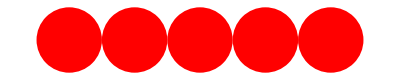

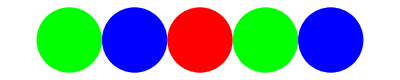
Za dodatni izziv poskusi napisati funkcijo MesaniKrogi[n], ki bo narisala kroge v izmenjajočih barvah. Na primer:
-Graphics-

Na podoben način definiraj še funkcijo NarisiKrogle[n], ki nariše n sfer. Sfere lahko postaviš tudi drugače (ne nujno v ravni vrsti).

Nariši interaktivni 3d graf, ki vsebuje tri zaporedne krogle, vsaki od katerih lahko spreminjaš njeno drugo koordinato.

-Graphics3D-

## Naloga 10

Napiši funkcijo, ki sprejme narvni števili m in n in vrne seznam prvih n členov Collatzovega zaporedja za število m. Pomagaj si s funkcijo “RecurrenceTable”.

```mathematica
Collatz[m_, n_]:=RecurrenceTable[
 { a[k + 1] == If[
Mod[a[k], 2] == 0,
Floor[a[k]/2],
3*a[k]+1
],
a[1] == m}
,a,{k,n}]
```

```mathematica
Collatz[18,25]
```

{18,9,28,14,7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1,4,2,1,4}